# Finite difference chronoamperometry

## Fully implicit method

This notebook shows how a chronoamperogram for the simple quasireversible reaction A + e ⇌ B can be simulated using finite difference methods.

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},(*PlotRange->{{1,n},{1,m},{0,1}},*)
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None}, 
FormatType-> TraditionalForm,
ImagePadding->{{Inherited,5},{Inherited,Inherited}},
PlotRegion-> {{0,1},{0.,1.}},
PlotLabel-> None 
(*Ticks-> {{0,0.2*n,0.4*n,0.6*n,0.8*n,n},{0,-0.5,-1.0,-1.5,-2.0,-2.5}}*)
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDiagonals];

makeDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[-d,{m-3}];
		z=Table[-d,{m-3}];
		y=Table[1.+2.*d,{m-2}];
{x,y,z}]
```

```mathematica
makeDiagonals[7,d]
```

{{-d,-d,-d,-d},{1.+2. d,1.+2. d,1.+2. d,1.+2. d,1.+2. d},{-d,-d,-d,-d}}

## Set Up Solution

```mathematica
Clear[implicitChronoAmp];

implicitChronoAmp[m_Integer,n_Integer,d_,{ksStar_,α_}][forwardStep_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext,ξ,tmp},
{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext:=Module[{tmp2,b},
b=#[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b[[-1]]+=d;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]]&;

ξ=Exp[forwardStep];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;

Rest@NestList[solveNext,initial,n-1]
]
```

```mathematica
implicitChronoAmp[m_Integer,n_Integer,d_,{ksStar_,α_}][forwardStep_,backwardStep_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext,ξ,tmp,cFor,cRev},
{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext:=Module[{tmp2,b},
b=#[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b[[-1]]+=d;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]]&;

ξ=Exp[forwardStep];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;

cFor=Rest@NestList[solveNext,initial,n-1];

ξ=Exp[backwardStep];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;

cRev=Rest[NestList[solveNext,Last[cFor],n-1]];

Join[cFor,cRev]
]
```

## Set Parameter Values

```mathematica
Clear[α,backwardStep,forwardStep,𝒟,n,𝔻,m,ksStar,c];

α=0.5;

backwardStep=10.(*step = f×(E-E^o)*);

forwardStep=-10.(*step = f×(E-E^o)*);

𝒟=1.*^-5;

n=200;

𝔻=2.;

m=Ceiling[6*√(𝔻*(n-1))];

ksStar=2.*^-3;(*dimensionless rate constant*)

initial=Table[1.,{j,1,m}];
```

## Solve

```mathematica
(*single potential step*)

c=implicitChronoAmp[m,n,𝔻,{ksStar,α}][forwardStep];
```

```mathematica
(*double potential step*)

c=implicitChronoAmp[m,n,𝔻,{ksStar,α}][forwardStep,backwardStep];
```

## Plot current v. time

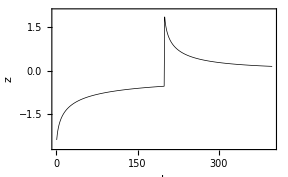

```mathematica
Clear[i];
i=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

ListPlot[i,optionA,PlotRange-> {{0, Length[i]}, { 1.1*Min[i],Max[1.1*Max[i],0]}}]
```